# Dynamical Correlation for Volterra Lattice

## Real Dynamics

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Parameter for Evolution

```mathematica
myBeta = 1.1;
myDeltax = 1/200;
myBetaList = {1,1.1,2.2,1.5,2.9,4.5};
myNumPoints = 1000;
SparseIdentityMatrix[n_]:=SparseArray[{i_,i_}:>1,{n,n}]
EE[j_,i_,n_]:= Array[Which[
#1== j && #2== i, 1,
True, 0
]&,{n,n}]
(*Distribution a_j^2*)
adistribution[β_,x_]:=1/Gamma[β/2] x^(β/2-1)Exp[- x];
Integrate[adistribution[β,x],{x,0,Infinity}]
2*Integrate[x*adistribution[β,x],{x,0,Infinity}]
Integrate[Log[x]*adistribution[β,x],{x,0,Infinity}]/2
FullSimplify[Integrate[x^2adistribution[β,x],{x,0,Infinity}]]
```

ConditionalExpression[1, Re[β]>0]

ConditionalExpression[(2 Gamma[(2+β)/2])/Gamma[β/2], Re[β]>-2]

ConditionalExpression[1/2 PolyGamma[0,β/2], Re[β]>0]

ConditionalExpression[1/4 β (2+β), Re[β]>-4]

## Statistical Time Correlations

```mathematica
(*average a_j log(a_j)*)
aavgdouble[β_] :=β
logavgmezzi[β_] :=1/2 PolyGamma[0,β/2]
(*Variance a, variance log(a), correlation a,log(a) *)
varadouble[β_] = FullSimplify[4*Integrate[x^2adistribution[β,x],{x,0,Infinity}] - β^2, Assumptions->β>0]
varloga[β_]  = FullSimplify[Integrate[Log[x]^2adistribution[β,x],{x,0,Infinity}] /4- logavgmezzi[β]^2, Assumptions->β>0] 
coraloga[β_] =FullSimplify[Integrate[x Log[x]adistribution[β,x],{x,0,Infinity}] - aavgdouble[β] logavgmezzi[β] ,Assumptions->{β>0}]
(* overall covariance matrix for stretch, momentum and energy *)
Cmat[β_]=FullSimplify[{{varadouble[β],coraloga[β]},{coraloga[β],varloga[β]}},Assumptions->{β>0}];
Cmat[myBeta] //MatrixForm
```

$Aborted

1/4 PolyGamma[1,β/2]

1

(2.2 | 1
1 | 1.05021)

## Free Energy

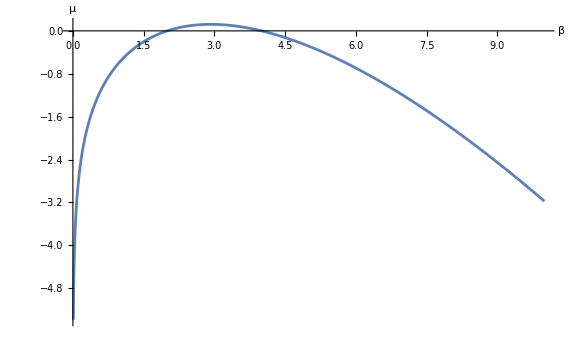

0

2.92326

```mathematica
VolterraF[β_]:= FullSimplify[-Log[Gamma[β/2]]];
Plot[VolterraF[x],{x,0,10},AxesLabel->{"β","μ"}]
FullSimplify[D[VolterraF[β],β] + logavgmezzi[β]]
(*Beta crit*)
BetaCrit =β/.Last[ FindMaximum[VolterraF[β],{β,2}]]
```

## Density of states for the Antisymmetric Gaussian Beta Ensemble

The density are correct, meaning that they are just on R+ and they are normalized to β

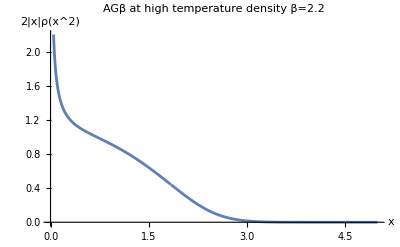

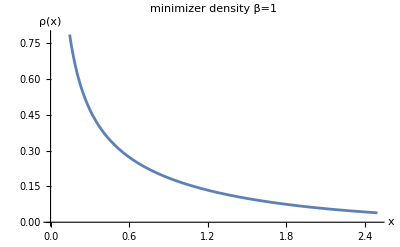

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 1.09349 and 0.00139873 for the integral and error estimates.

1.09349

```mathematica
(* density of the Antisymmetric Beta ensemble at high temperature normalized to β, see G.Mazzuca and P.J. Forrester : "The classical beta ensembles with beta proportional to 1/N:from loop- equations to Dyson's disordered chain." Journal of Mathematical Physics 62,073505 (2021).DOI:10.1063/5.0048481 *)
ρ[β_,x_]:= β/( Gamma[β/2]*Gamma[β/2+1]*Abs[WhittakerW[-β/2+1/2,0,-x]]^2);
(*Plots*)
With[{β=2.2},Plot[2*Abs[x]ρ[β,x^2],{x,0,5},PlotLabel->"AGβ at high temperature density β="<>ToString[β],AxesLabel->{"x","2|x|ρ(x^2)"}]]
With[{β=1},Plot[ρ[β,x],{x,0,myDeltax*(myNumPoints/2-1/2)},PlotLabel->"minimizer density β="<>ToString[β],AxesLabel->{"x","ρ(x)"}]]
(* evaluate on grid *)
With[{Δx=myDeltax,numpoints=myNumPoints},Module[{vlist= Δx*Range[1/2,  numpoints-1/2 ]},Table[Subscript[ρAGlist, β,Δx]=N[2*Abs[#]*ρ[β,#^2]]&/@vlist,{β,myBetaList}]]]; 
With[{Δx=myDeltax,numpoints=myNumPoints},Module[{vlist= Δx*Range[1/2,  numpoints - 1/2 ]},Table[Export["Measure_Antisym_Beta"<>ToString[N[β]]<>".csv",Transpose[{N[vlist],Subscript[ρAGlist, β,Δx]}]],{β,myBetaList}]]];
NIntegrate[2*x*ρ[myBeta,x^2],{x,0,Infinity}]
```

## Finite Element method for the approximation of the operator

The hat function base is just for x>0 since all the eigenvalues that I am considering lives just on the positive real axis

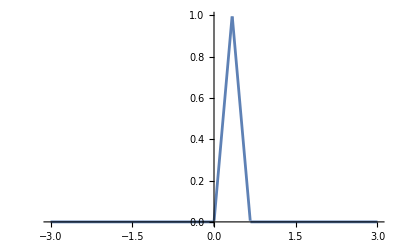

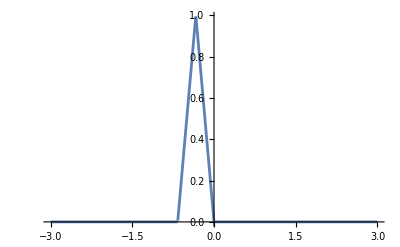

-Graphics-

```mathematica
HatFunction[h_,x_,k_]:=Piecewise[{{(x-(k-1)h)/h,(k-1)h≤x∧x<k h },{((k+1)h-x)/h,k h≤x∧x<h(k+1)}},0]
With[{h=1/3,k=1},Plot[HatFunction[h,x,k],{x,-3,3}]]
With[{h=1/3,k=-1},Plot[HatFunction[h,x,k],{x,-3,3}]]
With[{h=1/3,k=1},Plot[HatFunction[h,-x,k],{x,-3,3}]]
```

### Gram Matrix

```mathematica
(* overlap integrals *)
Integrate[HatFunction[h,x,0]^2,{x,-h,h},Assumptions->{h>0}]
Integrate[HatFunction[h,x,0]*HatFunction[h,x,1],{x,-h,2h},Assumptions->{h>0}]
Integrate[HatFunction[h,x,0]*HatFunction[h,x,2],{x,-h,3h},Assumptions->{h>0}]
```

(2 h)/3

h/6

0

```mathematica
HatGramMatrix[h_,numpoints_]:=h(2/3 IdentityMatrix[numpoints]+DiagonalMatrix[ConstantArray[1/6,numpoints-1],1]+DiagonalMatrix[ConstantArray[1/6,numpoints-1],-1]) - h/6 EE[2,1,numpoints]
(* example *)
HatGramMatrix[h,6]//MatrixForm
```

((2 h)/3 | h/6 | 0 | 0 | 0 | 0
0 | (2 h)/3 | h/6 | 0 | 0 | 0
0 | h/6 | (2 h)/3 | h/6 | 0 | 0
0 | 0 | h/6 | (2 h)/3 | h/6 | 0
0 | 0 | 0 | h/6 | (2 h)/3 | h/6
0 | 0 | 0 | 0 | h/6 | (2 h)/3)

### Scattering Integrals

They are the same as Christian, except for a factor 2

```mathematica
HatScatteringOverlap[h_,0]:= h^2 (2 Log[h]+8/3 Log[2]-25/6)/2
HatScatteringOverlap[h_,1]:=h^2 (2 Log[h]+27/4 Log[3]-25/6-16/3 Log[2])/2
HatScatteringOverlap[h_,2]:=h^2 (2 Log[h]+(152 Log[2])/3-27 Log[3]-25/6)/2
HatScatteringOverlap[h_,k_]:= h^2 (2Log[h]+1/2 k^4 Log[k]-1/3((k+1)^4 Log[k+1]+(k-1)^4 Log[k-1])+1/12((k+2)^4 Log[k+2]+(k-2)^4 Log[k-2])-25/6)/2
```

### Approximation of the operator T

```mathematica
(*T_{j,i}*)
T = ParallelTable[HatScatteringOverlap[myDeltax,Abs[i-j]] + HatScatteringOverlap[myDeltax,Abs[i+j]],{j,1,myNumPoints},{i,1,myNumPoints}] ;

(*Example*)
```

```mathematica
B= ParallelTable[HatScatteringOverlap[myDeltax,Abs[i-j]],{j,1,4},{i,1,4}]  + ParallelTable[HatScatteringOverlap[myDeltax,Abs[i+j+1]],{j,1,4},{i,1,4}];
B // MatrixForm
```

((-25/6+(8 Log[2])/3-2 Log[200])/80000+(-25/6+(81 Log[3])/2+1/3 (-16 Log[2]-256 Log[4])+(625 Log[5])/12-2 Log[200])/80000 | (-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+128 Log[4]+1/3 (-81 Log[3]-625 Log[5])+1/12 (16 Log[2]+1296 Log[6])-2 Log[200])/80000 | (-25/6+(152 Log[2])/3-27 Log[3]-2 Log[200])/80000+(-25/6+(625 Log[5])/2+1/3 (-256 Log[4]-1296 Log[6])+1/12 (81 Log[3]+2401 Log[7])-2 Log[200])/80000 | (-25/6+(81 Log[3])/2+1/3 (-16 Log[2]-256 Log[4])+(625 Log[5])/12-2 Log[200])/80000+(-25/6+648 Log[6]+1/3 (-625 Log[5]-2401 Log[7])+1/12 (256 Log[4]+4096 Log[8])-2 Log[200])/80000
(-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+128 Log[4]+1/3 (-81 Log[3]-625 Log[5])+1/12 (16 Log[2]+1296 Log[6])-2 Log[200])/80000 | (-25/6+(8 Log[2])/3-2 Log[200])/80000+(-25/6+(625 Log[5])/2+1/3 (-256 Log[4]-1296 Log[6])+1/12 (81 Log[3]+2401 Log[7])-2 Log[200])/80000 | (-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+648 Log[6]+1/3 (-625 Log[5]-2401 Log[7])+1/12 (256 Log[4]+4096 Log[8])-2 Log[200])/80000 | (-25/6+(152 Log[2])/3-27 Log[3]-2 Log[200])/80000+(-25/6+(2401 Log[7])/2+1/3 (-1296 Log[6]-4096 Log[8])+1/12 (625 Log[5]+6561 Log[9])-2 Log[200])/80000
(-25/6+(152 Log[2])/3-27 Log[3]-2 Log[200])/80000+(-25/6+(625 Log[5])/2+1/3 (-256 Log[4]-1296 Log[6])+1/12 (81 Log[3]+2401 Log[7])-2 Log[200])/80000 | (-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+648 Log[6]+1/3 (-625 Log[5]-2401 Log[7])+1/12 (256 Log[4]+4096 Log[8])-2 Log[200])/80000 | (-25/6+(8 Log[2])/3-2 Log[200])/80000+(-25/6+(2401 Log[7])/2+1/3 (-1296 Log[6]-4096 Log[8])+1/12 (625 Log[5]+6561 Log[9])-2 Log[200])/80000 | (-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+2048 Log[8]+1/3 (-2401 Log[7]-6561 Log[9])+1/12 (1296 Log[6]+10000 Log[10])-2 Log[200])/80000
(-25/6+(81 Log[3])/2+1/3 (-16 Log[2]-256 Log[4])+(625 Log[5])/12-2 Log[200])/80000+(-25/6+648 Log[6]+1/3 (-625 Log[5]-2401 Log[7])+1/12 (256 Log[4]+4096 Log[8])-2 Log[200])/80000 | (-25/6+(152 Log[2])/3-27 Log[3]-2 Log[200])/80000+(-25/6+(2401 Log[7])/2+1/3 (-1296 Log[6]-4096 Log[8])+1/12 (625 Log[5]+6561 Log[9])-2 Log[200])/80000 | (-25/6-(16 Log[2])/3+(27 Log[3])/4-2 Log[200])/80000+(-25/6+2048 Log[8]+1/3 (-2401 Log[7]-6561 Log[9])+1/12 (1296 Log[6]+10000 Log[10])-2 Log[200])/80000 | (-25/6+(8 Log[2])/3-2 Log[200])/80000+(-25/6+(6561 Log[9])/2+1/3 (-4096 Log[8]-10000 Log[10])+1/12 (2401 Log[7]+14641 Log[11])-2 Log[200])/80000)

### Dressing Transform

```mathematica
G=HatGramMatrix[myDeltax,myNumPoints];
DressingTransformation[Δx_,ρ_List,ψ_List]:=Module[{numpoints=Length[ρ],vlist},vlist=Δx*Range[1/2, numpoints-1/2 ];
ψdr =LinearSolve[G-T.DiagonalMatrix[ρ],G.ψ]];
```

```mathematica
Length[Subscript[ρAGlist, myBeta,myDeltax]]
Length[T]
```

1000

1000

## Computation of quantities useful for the correlations function

Something is wrong with the dimension of the array, check that

### [1]^dr

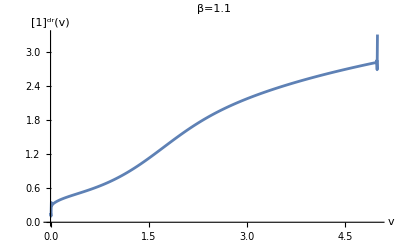

```mathematica
With[{BetaList=myBetaList,Δx=myDeltax,numpoints=myNumPoints},Table[Subscript[onedr, β,Δx]=DressingTransformation[Δx,Subscript[ρAGlist, β,Δx],ConstantArray[1,numpoints]],{β,BetaList}]];
(* example *)
With[{β=myBeta,Δx=myDeltax,numpoints=myNumPoints},
Module[{vlist= Δx*Range[1/2,  numpoints - 1/2 ]},  
ListLinePlot[Transpose[{vlist,Subscript[onedr, β,Δx]}],AxesLabel->{"v","[1]^dr(v)"},PlotLabel->"β="<>ToString[β]]]]
```

### σ - density of states for the Volterra Lattice

```mathematica
With[{βList=myBetaList,Δx=myDeltax},Table[Subscript[σ, β,Δx]=Subscript[ρAGlist, β,Δx] Subscript[onedr, β,Δx],{β,βList}]];
f[β]=D[VolterraF[β],β]
Table[Subscript[κ, β] =N[-2*logavgmezzi[β]] ,{β,myBetaList}]

(* example *)
(*With[{β=myBeta,Δx=myDeltax,numpoints=myNumPoints},
Module[{vlist= Δx*Range[+1/2,  numpoints-1/2 ]},
res = NIntegrate[Interpolation[Transpose[{vlist,Subscript[σ, β,Δx]}],InterpolationOrder->5][x],{x,Δx/2,(numpoints-1/2)*Δx}];
Print[N[Subscript[κ, β]*res]]; 
Print[N[1/Subscript[κ, β]]];
vlist = N[vlist];
ListLinePlot[Transpose[{vlist,Subscript[σ, β,Δx]}],AxesLabel->{"v","σ(v)"},PlotLabel->"β="<>ToString[β]]]]*)
```

-1/2 PolyGamma[0,β/2]

{1.96351,1.73596,0.423755,1.08586,0.0113164,-0.572546}

```mathematica
(*With[{β=4.5,Δx=myDeltax,numpoints=myNumPoints},
vlist= Δx*Range[+1/2,  numpoints-1/2 ];
res = NIntegrate[Interpolation[Transpose[{vlist,Subscript[σ, β,Δx]}],InterpolationOrder->3][x],{x,(1/2)*Δx,(numpoints+1/2)*Δx}];
Print[res*Subscript[κ, β]];
ListLinePlot[Transpose[{vlist,Subscript[σ, β,Δx]}],AxesLabel->{"v","σ(v)"},PlotLabel->"β="<>ToString[β]]]*)
```

### [v^2]^dr

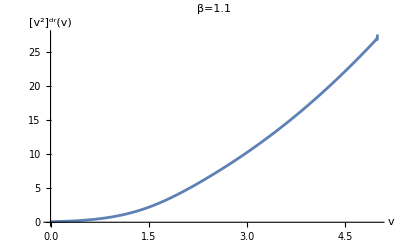

```mathematica
With[{βList=myBetaList,Δx=myDeltax,numpoints=myNumPoints},Module[{vlist=( Δx*Range[+1/2,  numpoints-1/2 ])^2},Table[Subscript[vdr, β,Δx]=DressingTransformation[Δx,Subscript[ρAGlist, β,Δx],vlist],{β,myBetaList}]]];
(* example *)
With[{β=myBeta,Δx=myDeltax,numpoints=myNumPoints},Module[{vlist= Δx*Range[+1/2,  numpoints-1/2 ]},ListLinePlot[Transpose[{vlist,Subscript[vdr, β,Δx]}],AxesLabel->{"v","[v^2]^dr(v)"},PlotLabel->"β="<>ToString[β]]]]
```

### κ_β

```mathematica
(* use the free energy to compute it*)
D[VolterraF[x],x];
Table[Subscript[κ, β] =-2N[logavgmezzi[β]] ,{β,myBetaList}]
```

{1.96351,1.73596,0.423755,1.08586,0.0113164,-0.572546}

### q_1

```mathematica
With[{βlist = myBetaList}, Table[Subscript[q, 1,β]=aavgdouble[ β], {β,βlist}]]
```

{1,1.1,2.2,1.5,2.9,4.5}

### ([w]^dr-q_1[1]^dr)

```mathematica
With[{βlist = myBetaList,Δx=myDeltax}, Table[Subscript[aterm, β,Δx]=(Subscript[vdr, β,Δx]- Subscript[q, 1,β]*Subscript[onedr, β,Δx]),  {β,βlist}]];
```

### Effective Velocity

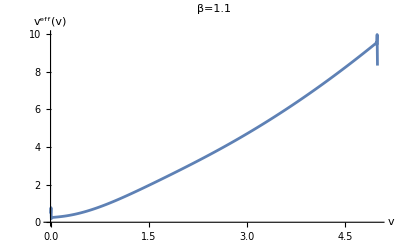

```mathematica
With[{βlist=myBetaList,Δx=myDeltax},Table[Subscript[veff, β,Δx]=Subscript[vdr, β,Δx]/Subscript[onedr, β,Δx],{β,βlist}]];
(* example *)
With[{β=myBeta,Δx=myDeltax,numpoints=myNumPoints},Module[{vlist= Δx*Range[+1/2,  numpoints-1/2 ]},
ListLinePlot[Transpose[{vlist,Subscript[veff, β,Δx]}],AxesLabel->{"v","v^eff(v)"},PlotLabel->"β="<>ToString[β]]]]
```

### Inversion

```mathematica
With[{βlist=myBetaList,Δx=myDeltax},Table[Subscript[xnew, β,Δx]=(Subscript[veff, β,Δx]-Subscript[q, 1,β] )/( Subscript[κ, β]),{β,βlist}]];
(*Example*)
With[{β=myBeta,Δx=myDeltax,numpoints=myNumPoints},Module[{vlist=Δx*Range[1/2, numpoints - 1/2 ]},
ListLinePlot[Transpose[{vlist,(Subscript[veff, β,Δx] -Subscript[q, 1,β])/(Subscript[κ, β])}],AxesLabel->{"v","(ṽ)^eff(v)"},PlotLabel->"β="<>ToString[β]]]
Print[Length[Subscript[xnew, β,Δx]]];]
```

1000

### Dynamical Correlation

The dynamical correlation functions depends on the condition that x + t(v_eff-q_1)/κ=0, except for a uniform scaling 1/t

```mathematica
Print[Length[Subscript[xnew, myBeta,myDeltax]]]
With[{βlist=myBetaList,Δx=myDeltax,numpoints=myNumPoints},Module[{vlist=Δx*Range[1/2, numpoints-1/2 ],vefftildeip,αlist},Table[αlist={-Subscript[onedr, β,Δx] * Subscript[κ, β],Subscript[aterm, β,Δx]};Table[vefftildeip=Interpolation[Transpose[{vlist,Subscript[xnew, β,Δx]}]];
Subscript[S, i,j,β,Δx]=Transpose[{(* resolving δ-function results in (ṽ)^eff for x/t *)Subscript[xnew, β,Δx],Subscript[κ, β]/Abs[vefftildeip'[#]&/@vlist] *Subscript[σ, β,Δx] *αlist⟦i+1⟧*αlist⟦j+1⟧}],{i,0,1},{j,0,1}], {β,βlist}]]];
```

1000

```mathematica
With[{Δx=myDeltax},Table[Export["Volterra_correlations_Beta"<>ToString[N[β]]<>"_S00.csv",Subscript[S, 0,0,β,Δx]],{β,myBetaList}];
Table[Export["Volterra_correlations_Beta"<>ToString[N[β]]<>"_S01.csv",Subscript[S, 0,1,β,Δx]],{β,myBetaList}];
Table[Export["Volterra_correlations_Beta"<>ToString[N[β]]<>"_S11.csv",Subscript[S, 1,1,β,Δx]],{β,myBetaList}];]
```

Transpose::nmtx: The first two levels of {{1/400,3/400,1/80,7/400,9/400,11/400,13/400,3/80,17/400,19/400,«990»},xnew_(β,1/200)} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{1/400,3/400,1/80,7/400,9/400,11/400,13/400,3/80,17/400,19/400,«990»},xnew_(β,1/200)}] does not contain a list of data and coordinates.

Part::partd: Part specification αlist$99215⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Subscript[xnew, <<2>>], {Divide[Power[αlist$99215[[1]], 2] Subscript[κ, β] Subscript[σ, <<2>>], Abs[(Interpolation[Transpose[{{<<1000>>}, Subscript[xnew, <<2>>]}]])'[<<1>>]]], <<998>>, Divide[Power[αlist$99215[[1]], 2] <<9>>[<<2>>] Subscript[σ, <<2>>], <<1>>]}} cannot be transposed.

Transpose::nmtx: The first two levels of {{1/400,3/400,1/80,7/400,9/400,11/400,13/400,3/80,17/400,19/400,«990»},xnew_(β,1/200)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{{1/400,3/400,1/80,7/400,9/400,11/400,13/400,3/80,17/400,19/400,«990»},xnew_(β,1/200)}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Part::partd: Part specification αlist$99215⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::nliter: Non-list iterator Print[Length[xnew_(β,1/200)]];Table[vefftildeip$99215=Interpolation[Transpose[{vlist$99215,Subscript[«3»]}]];S_(i,j,β,1/200)=Transpose[{xnew_(β,1/200),«2» Subscript[«3»] Subscript[«2»] Part[«2»] Part[«2»]}],{i,0,1},{j,0,1}] at position 2 does not evaluate to a real numeric value.

3

Table::nliter: Non-list iterator Print[Length[xnew_(β,1/200)]];Table[vefftildeip$99215=Interpolation[Transpose[{vlist$99215,Subscript[«3»]}]];S_(i,j,β,1/200)=Transpose[{xnew_(β,1/200),«2» Subscript[«3»] Subscript[«2»] Part[«2»] Part[«2»]}],{i,0,1},{j,0,1}] at position 2 does not evaluate to a real numeric value.

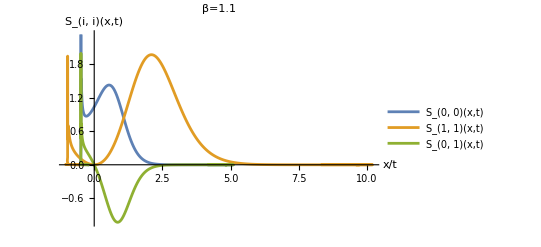

```mathematica
(* example *)
With[{β=1.1,Δx=myDeltax},ListLinePlot[{Subscript[S, 0,0,β,Δx],2*Subscript[S, 1,1,β,Δx],Subscript[S, 0,1,β,Δx]},PlotRange->Automatic,AxesLabel->{"x/t","S_(i, i)(x,t)"},PlotLegends->Placed[{"S_(0, 0)(x,t)","S_(1, 1)(x,t)","S_(0, 1)(x,t)"},Above],PlotLabel->"β="<>ToString[β]]]
```

## Check Integrals

```mathematica
With[{β=myBeta, Δx=myDeltax,numpoints=myNumPoints},  
tmp = NIntegrate[Interpolation[Transpose[{vlist,Subscript[σ, β,Δx]}],InterpolationOrder->3][x],{x,-numpoints*Δx,numpoints*Δx}];res = NIntegrate[x^4Interpolation[Transpose[{vlist,Subscript[σ, β,Δx]}],InterpolationOrder->3][x],{x,-numpoints*Δx,numpoints*Δx}]/tmp - (NIntegrate[x^2Interpolation[Transpose[{vlist,Subscript[σ, β,Δx]}],InterpolationOrder->3][x],{x,-numpoints*Δx,numpoints*Δx}]/tmp)^2]
```

34.8149

```mathematica
Length[Range[-6+1/2,  6-1/2 ]]
```

12

```mathematica
logavgmezzi[2.2]
```

-0.211877

```mathematica
NIntegrate[x*ρ[myBeta,x],{x,0,Infinity}]
```

0.605

```mathematica
2*Integrate[x*adistribution[β,x],{x,0,Infinity}]
```

ConditionalExpression[(2 Gamma[(2+β)/2])/Gamma[β/2], Re[β]>-2]